```mathematica
dir="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\"<>"AveragePicture\\";
SetDirectory[dir];
list=FileNames["*.jpg"];
tf=Length[list];
Print[tf]
```

34

```mathematica
$HistoryLength=0;
```

1

{3216,2136}

{3216,2136}

here1

here2

9/77

{3216,2136}

here3

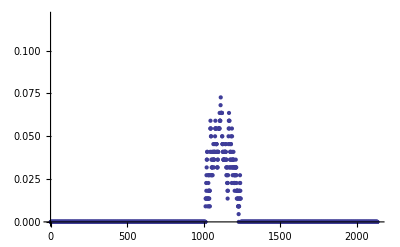
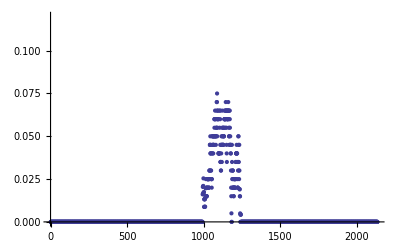
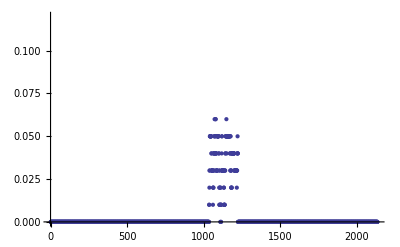
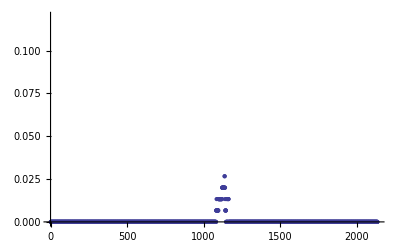
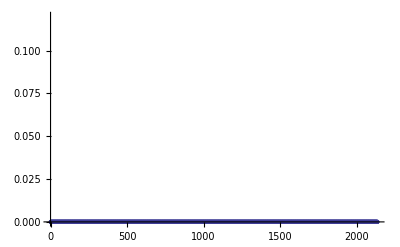
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-^2

2

{3216,2136}

{3216,2136}

here1

here2

14/103

{3216,2136}

here3

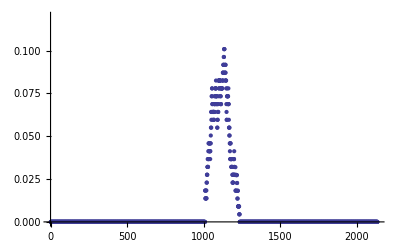
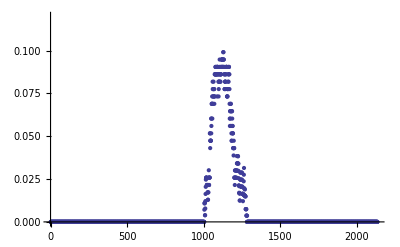
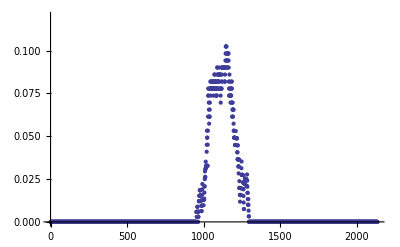
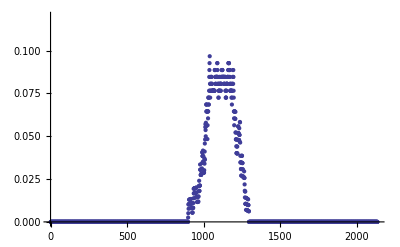
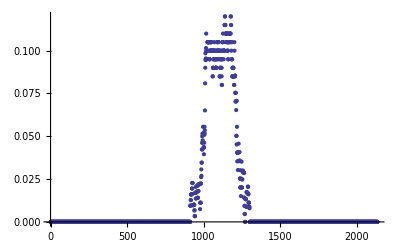
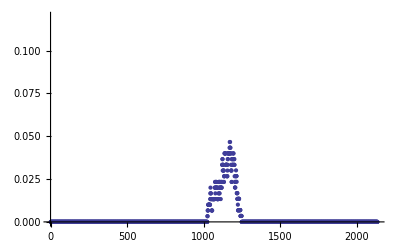
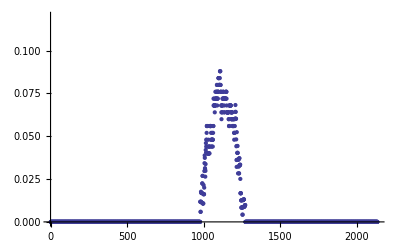

3

{3216,2136}

{3216,2136}

here1

here2

25/214

{3216,2136}

here3

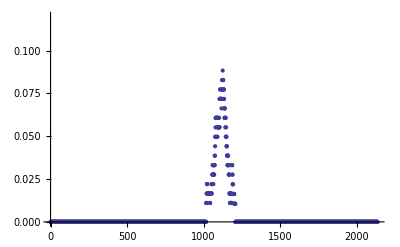
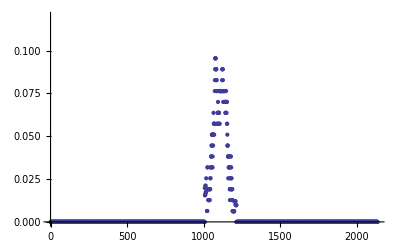
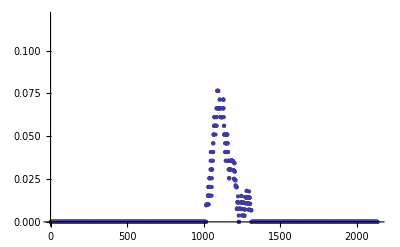
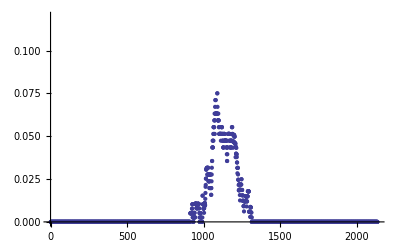
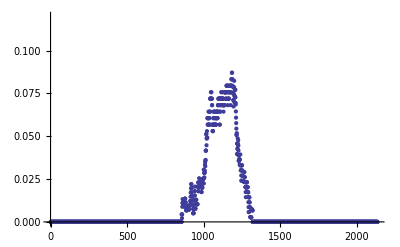
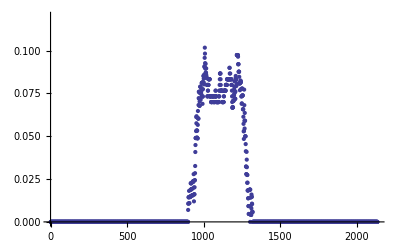
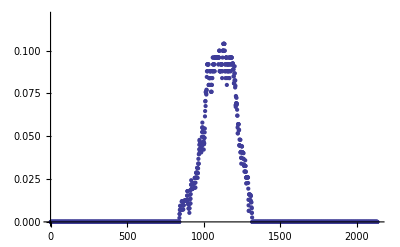

4

{3216,2136}

{3216,2136}

here1

here2

14/135

{3216,2136}

here3

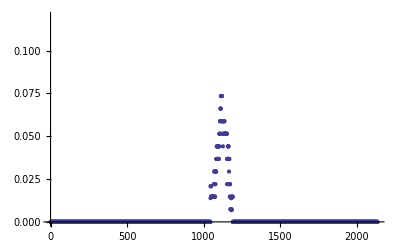
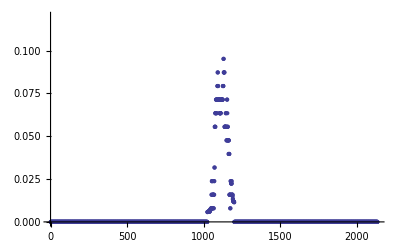
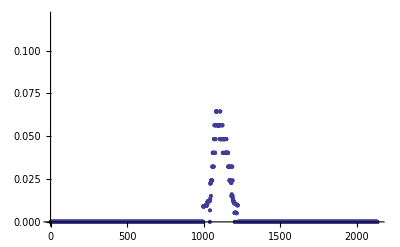
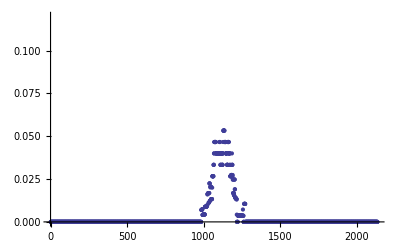
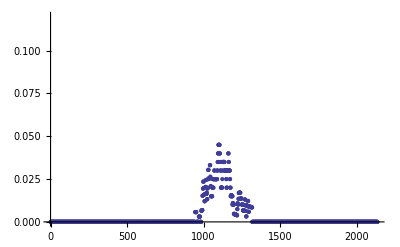
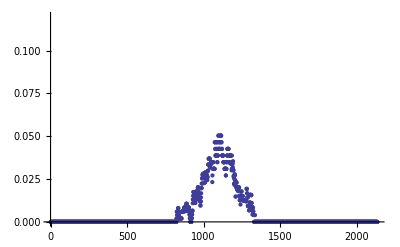
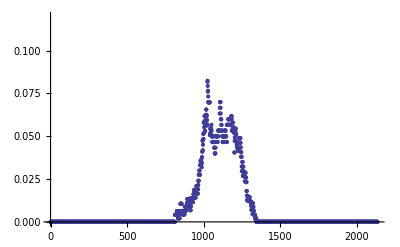

5

{3216,2136}

{3216,2136}

here1

here2

10/97

{3216,2136}

here3

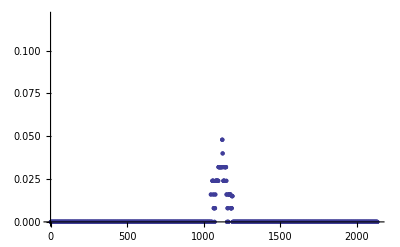
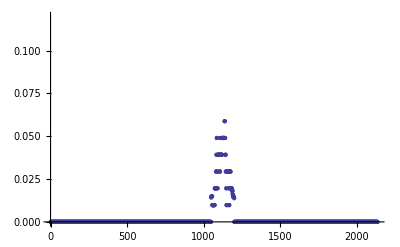
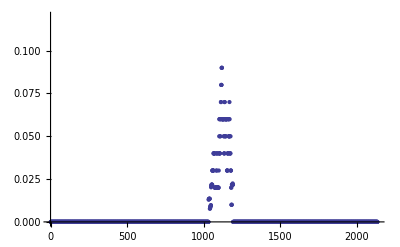
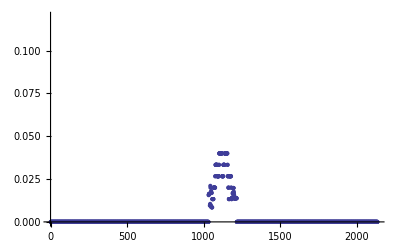
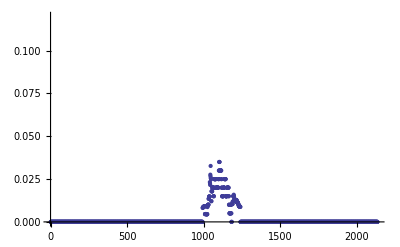
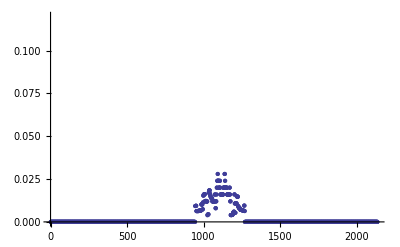
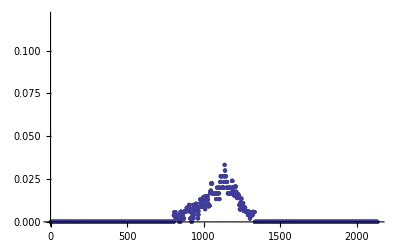

6

{3216,2136}

{3216,2136}

here1

here2

19/364

{3216,2136}

here3

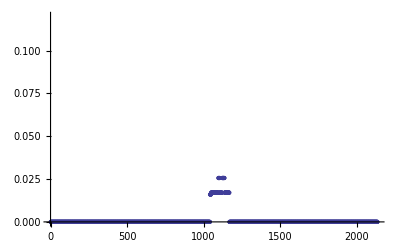
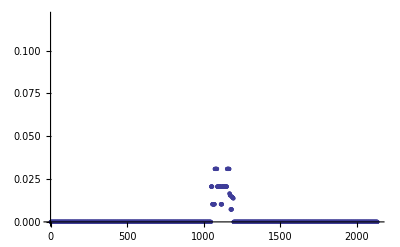
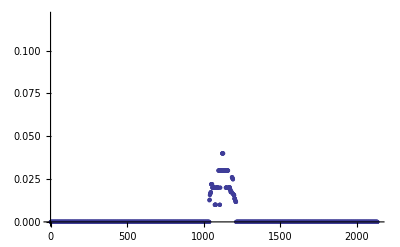
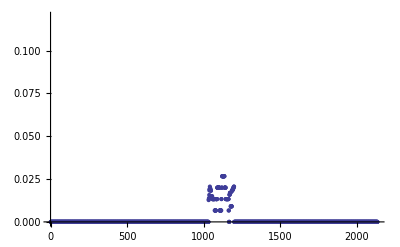
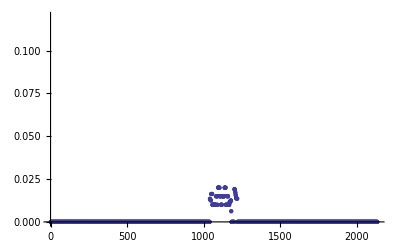
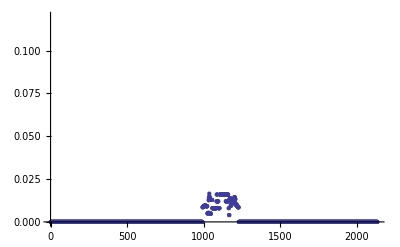
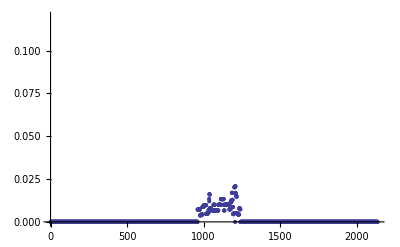

7

{3216,2136}

{3216,2136}

here1

here2

3/50

{3216,2136}

here3

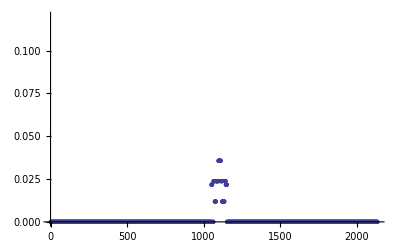
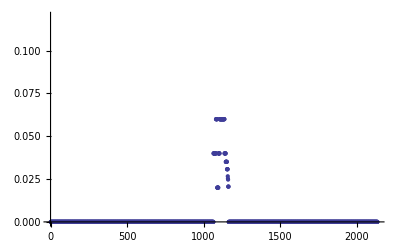
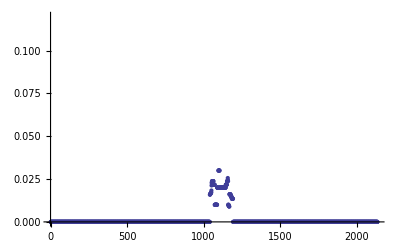
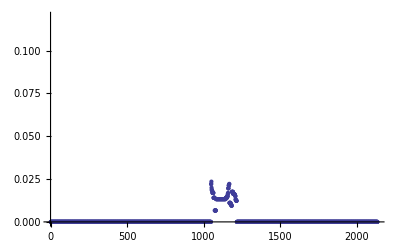
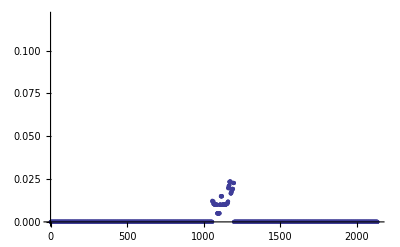
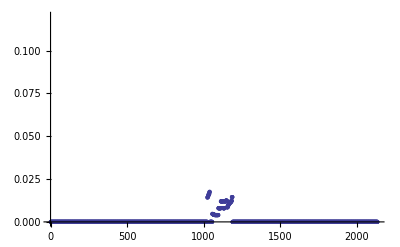
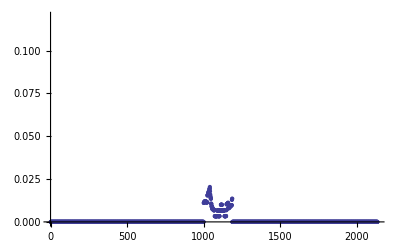

8

{3216,2136}

{3216,2136}

here1

here2

1/12

{3216,2136}

here3

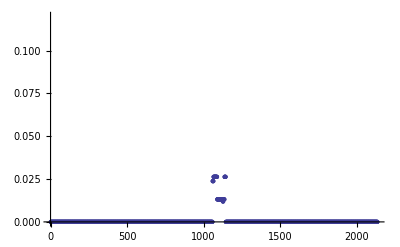
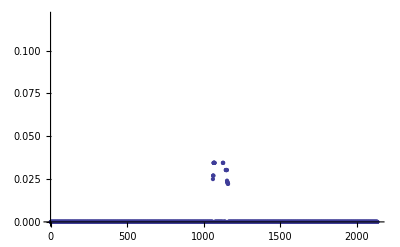
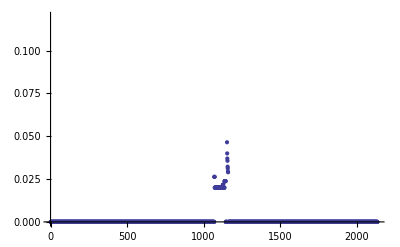
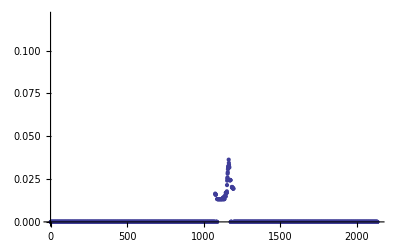
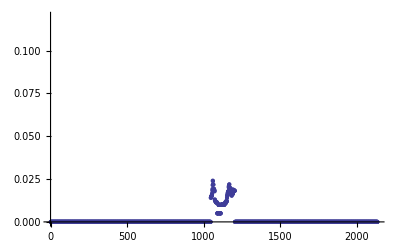
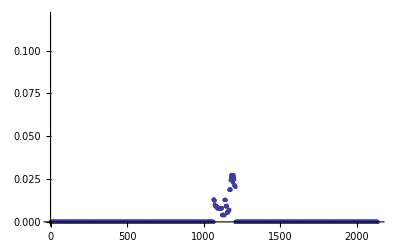
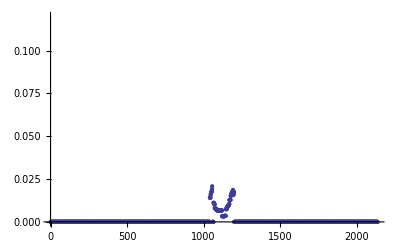

9

{3216,2136}

{3216,2136}

here1

here2

1/3

{3216,2136}

here3

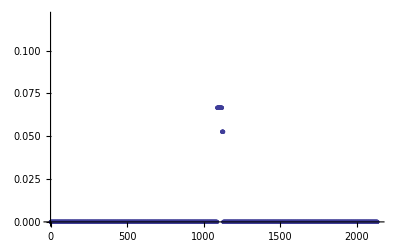
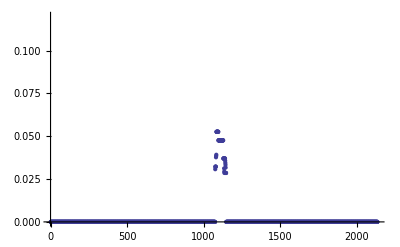
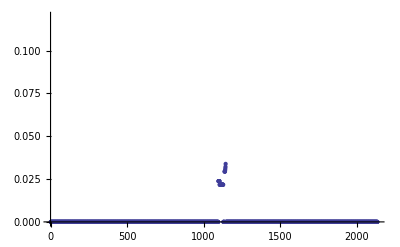
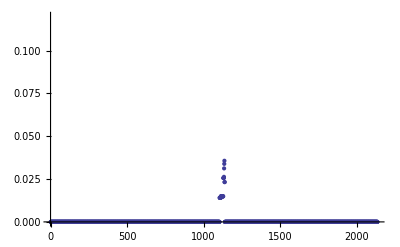
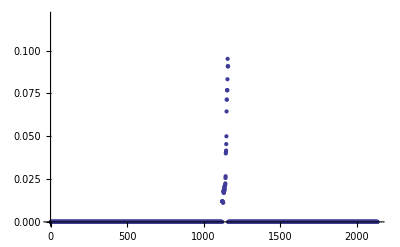
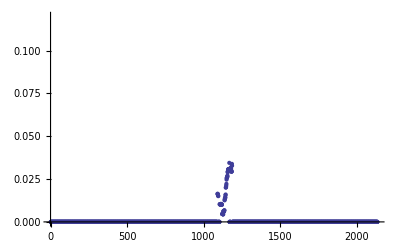
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics- -Graphics-

10

{3216,2136}

{3216,2136}

here1

here2

1/2

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-^2

11

{3216,2136}

{3216,2136}

here1

here2

1/4

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-^2

12

{3216,2136}

{3216,2136}

here1

here2

1

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-^2

13

{3216,2136}

{3216,2136}

here1

here2

1/5

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-^2

14

{3216,2136}

{3216,2136}

here1

here2

2

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-^2

15

{3216,2136}

{3216,2136}

here1

here2

2/3

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-^2

16

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-^2

17

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-^2

18

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-^2

19

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-^2

20

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-^2

21

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

22

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

23

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

24

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

25

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

26

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

27

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

28

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

29

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

30

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

31

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

32

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

33

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

34

{3216,2136}

{3216,2136}

here1

here2

0

{3216,2136}

here3

-Graphics--Graphics--Graphics--Graphics--Graphics-(-Graphics-)^2

```mathematica
For[i=1,i<tf+1,i=i+1,
Print[i];
file=dir<>"data"<>ToString[i]<>".jpg";
img=Import[file];
{w,h}=ImageDimensions[img];

Binary=Binarize[img,0.004];
Binary=ImageMultiply[Binary,CommonestFilter[Binary,20]];
bn=ImageData[Binary];


rb=Total[bn,{2}]/2;
rbb=Transpose[Table[rb,{i,1,w}]];
Print[Dimensions[rbb]];
ClearAll[rb];

Cumulative=Accumulate[bn];
ClearAll[bn];
Print[Dimensions[Cumulative]];

FindCentre=Cumulative-rbb;
Firsthalf=FindCentre/.x_/;x<0->0;
FirsthalfBinary=Firsthalf/.x_/;x>0->1;
ClearAll[Firsthalf];
ThicknessFirsthalf=Cumulative*FirsthalfBinary;
ClearAll[FirsthalfBinary];

Secondhalf=FindCentre/.x_/;x>0->0;
ClearAll[FindCentre];
SecondhalfBinary=Secondhalf/.x_/;x<0->1;
ClearAll[Secondhalf];
ThicknessSecondhalf=2*rbb-Cumulative;
ClearAll[rbb,Cumulative];

ThicknessSecondhalf=ThicknessSecondhalf*SecondhalfBinary;
ClearAll[SecondhalfBinary];

ThicknessFinal=ThicknessFirsthalf+ThicknessSecondhalf;
ThicknessFinal=ThicknessFinal/.{0->10^11};
ClearAll[ThicknessFirsthalf,ThicknessSecondhalf];

img=ImageMultiply[img,Binary];
{r,g,b}=ColorSeparate[img];
ClearAll[img,file,g,b];

Print["here1"];
r=ImageData[r,"Byte"];
Print["here2"];
r=r/ThicknessFinal;
ClearAll[ThicknessFinal];
(*g=g/ThicknessFinal;
b=b/ThicknessFinal;*)
Print[Max[r]];
Print[Dimensions[r]];

Print["here3"];
Print[ListPlot[Part[r,10], PlotRange->{{0,w},{0,0.12}}],ListPlot[Part[r,50], PlotRange->{{0,w},{0,0.12}}],ListPlot[Part[r,100], PlotRange->{{0,w},{0,0.12}}],ListPlot[Part[r,150], PlotRange->{{0,w},{0,0.12}}],ListPlot[Part[r,200], PlotRange->{{0,w},{0,0.12}}],ListPlot[Part[r,250], PlotRange->{{0,w},{0,0.12}}]ListPlot[Part[r,300], PlotRange->{{0,w},{0,0.12}}]];

(*gd=ImageResize[g,500];
gd=ImageData[gd];
MaxG=Max[gd];
MinG=Min[gd];

bd=ImageResize[b,500];
bd=ImageData[bd];
MaxB=Max[bd];
MinB=Min[bd];*);


]
```

```mathematica
(*For[i=16,i<tf+1,i=i+1,
Print[i];
file=dir<>"data"<>ToString[i]<>".jpg";
img=Import[file];
{w,h}=ImageDimensions[img];

Binary=Binarize[img,0.004];
Binary=ImageMultiply[Binary,CommonestFilter[Binary,20]];
bn=ImageData[Binary];


rb=Total[bn,{2}]/2;
rbb=Transpose[Table[rb,{i,1,w}]];
Print[Dimensions[rbb]];
ClearAll[rb];

Cumulative=Accumulate[bn];
ClearAll[bn];
Print[Dimensions[Cumulative]];

FindCentre=Cumulative-rbb;
Firsthalf=FindCentre/.x_/;x<0->0;
FirsthalfBinary=Firsthalf/.x_/;x>0->1;
ClearAll[Firsthalf];
ThicknessFirsthalf=Cumulative*FirsthalfBinary;
ClearAll[FirsthalfBinary];

Secondhalf=FindCentre/.x_/;x>0->0;
ClearAll[FindCentre];
SecondhalfBinary=Secondhalf/.x_/;x<0->1;
ClearAll[Secondhalf];
ThicknessSecondhalf=2*rbb-Cumulative;
ClearAll[rbb,Cumulative];

ThicknessSecondhalf=ThicknessSecondhalf*SecondhalfBinary;
ClearAll[SecondhalfBinary];

ThicknessFinal=ThicknessFirsthalf+ThicknessSecondhalf;
ThicknessFinal=ThicknessFinal/.{0->10^11};
ClearAll[ThicknessFirsthalf,ThicknessSecondhalf];

img=ImageMultiply[img,Binary];
{r,g,b}=ColorSeparate[img];
ClearAll[img,file,r,b];

Print["here1"];
gim=ImageData[g,"Byte"];
Print["here2"];
g=gim/ThicknessFinal;
(*g=g/ThicknessFinal;
b=b/ThicknessFinal;*)
Print[g[[500,1000]]];
Print[gim[[500,1000]]];
Print[Dimensions[gim]];
Print[Dimensions[g]];
gim=Image[gim];
Print["problem"];
g=Image[g];

Print["here3"];
ClearAll[ThicknessFinal];

gd=ImageResize[g,500];
gd=ImageData[gd];
Print[gd[[600,200]]];
MaxG=Max[gd];
MinG=Min[gd];

(*gd=ImageResize[g,500];
gd=ImageData[gd];
MaxG=Max[gd];
MinG=Min[gd];

bd=ImageResize[b,500];
bd=ImageData[bd];
MaxB=Max[bd];
MinB=Min[bd];*);

Needs["PlotLegends`"];
Print["packagedownload"];
(*ri=ShowLegend[ListDensityPlot[rd,ColorFunction->"Rainbow", PlotRange->All],{ColorData["Rainbow"][#1]&,10,ToString[MinR*255],ToString[MaxR*255], LegendPosition->{1.1,-0.4}}];
Print["ri created"];
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\"<>"AverageConcContoursRed\\";
file=dir1<>"dataR"<>ToString[i]<>".jpg";
Export[file,ri];
ClearAll[file,ri,rd,MaxR,MinR]*);

gi=ShowLegend[ListDensityPlot[gd,ColorFunction->"Rainbow", PlotRange->All],{ColorData["Rainbow"][#1]&,10,ToString[MinG*255],ToString[MaxG*255], LegendPosition->{1.1,-0.4}}];
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\"<>"AverageConcContoursGreen\\";
file=dir1<>"dataG"<>ToString[i]<>".jpg";
Export[file,gi];
ClearAll[file,gi,gd,MaxG,MinG];

(*bi=ShowLegend[ListDensityPlot[bd,ColorFunction->"Rainbow", PlotRange->All],{ColorData["Rainbow"][#1]&,10,ToString[MaxB*255],ToString[MinB*255], LegendPosition->{1.1,-0.4}}];
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\"<>"AverageConcContoursBlue\\";
file=dir1<>"dataB"<>ToString[i]<>".jpg";
Export[file,bi];
ClearAll[file,bi,bd,MaxB,MinB];*)
]*)
```

```mathematica
(*For[i=1,i<tf+1,i=i+1,
Print[i];
file=dir<>"data"<>ToString[i]<>".jpg";
img=Import[file];
{w,h}=ImageDimensions[img];

Binary=Binarize[img,0.004];
Binary=ImageMultiply[Binary,CommonestFilter[Binary,20]];
bn=ImageData[Binary];


rb=Total[bn,{2}]/2;
rbb=Transpose[Table[rb,{i,1,w}]];
Print[Dimensions[rbb]];
ClearAll[rb];

Cumulative=Accumulate[bn];
ClearAll[bn];
Print[Dimensions[Cumulative]];

FindCentre=Cumulative-rbb;
Firsthalf=FindCentre/.x_/;x<0->0;
FirsthalfBinary=Firsthalf/.x_/;x>0->1;
ClearAll[Firsthalf];
ThicknessFirsthalf=Cumulative*FirsthalfBinary;
ClearAll[FirsthalfBinary];

Secondhalf=FindCentre/.x_/;x>0->0;
ClearAll[FindCentre];
SecondhalfBinary=Secondhalf/.x_/;x<0->1;
ClearAll[Secondhalf];
ThicknessSecondhalf=2*rbb-Cumulative;
ClearAll[rbb,Cumulative];

ThicknessSecondhalf=ThicknessSecondhalf*SecondhalfBinary;
ClearAll[SecondhalfBinary];

ThicknessFinal=ThicknessFirsthalf+ThicknessSecondhalf;
ThicknessFinal=ThicknessFinal/.{0->10^11};
ClearAll[ThicknessFirsthalf,ThicknessSecondhalf];

img=ImageMultiply[img,Binary];
{r,g,b}=ColorSeparate[img];
ClearAll[img,file,r,g];

Print["here1"];
bim=ImageData[b,"Byte"];
Print["here2"];
b=bim/ThicknessFinal;
(*g=g/ThicknessFinal;
b=b/ThicknessFinal;*)
Print[b[[500,1000]]];
Print[bim[[500,1000]]];
Print[Dimensions[bim]];
Print[Dimensions[b]];
bim=Image[bim];
Print["problem"];
b=Image[b];

Print["here3"];
ClearAll[ThicknessFinal];

bd=ImageResize[b,500];
bd=ImageData[bd];
Print[bd[[600,200]]];
MaxB=Max[bd];
MinB=Min[bd];

(*gd=ImageResize[g,500];
gd=ImageData[gd];
MaxG=Max[gd];
MinG=Min[gd];

bd=ImageResize[b,500];
bd=ImageData[bd];
MaxB=Max[bd];
MinB=Min[bd];*)

Needs["PlotLegends`"];
Print["packagedownload"];
(*ri=ShowLegend[ListDensityPlot[rd,ColorFunction->"Rainbow", PlotRange->All],{ColorData["Rainbow"][#1]&,10,ToString[MinR*255],ToString[MaxR*255], LegendPosition->{1.1,-0.4}}];
Print["ri created"];
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\"<>"AverageConcContoursRed\\";
file=dir1<>"dataR"<>ToString[i]<>".jpg";
Export[file,ri];
ClearAll[file,ri,rd,MaxR,MinR];*)

(*gi=ShowLegend[ListDensityPlot[gd,ColorFunction->"Rainbow", PlotRange->All],{ColorData["Rainbow"][#1]&,10,ToString[MaxG*255],ToString[MinG*255], LegendPosition->{1.1,-0.4}}];
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\"<>"AverageConcContoursGreen\\";
file=dir1<>"dataG"<>ToString[i]<>".jpg";
Export[file,gi];
ClearAll[file,gi,gd,MaxG,MinG];*)

bi=ShowLegend[ListDensityPlot[bd,ColorFunction->"Rainbow", PlotRange->All],{ColorData["Rainbow"][#1]&,10,ToString[MinB*255],ToString[MaxB*255], LegendPosition->{1.1,-0.4}}];
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\"<>"AverageConcContoursBlue\\";
file=dir1<>"dataB"<>ToString[i]<>".jpg";
Export[file,bi];
ClearAll[file,bi,bd,MaxB,MinB];
]*)
```